```mathematica
(* Rotation matrix *)
R1 = RotationMatrix[phi, {0, 0, 1}];
R2 = RotationMatrix[-theta, {0, 1, 0}];
R3 = RotationMatrix[-phi, {0, 0, 1}];
R = R1.R2.R3
```

{{Cos[phi]^2 Cos[theta]+Sin[phi]^2,-Cos[phi] Sin[phi]+Cos[phi] Cos[theta] Sin[phi],-Cos[phi] Sin[theta]},{-Cos[phi] Sin[phi]+Cos[phi] Cos[theta] Sin[phi],Cos[phi]^2+Cos[theta] Sin[phi]^2,-Sin[phi] Sin[theta]},{Cos[phi] Sin[theta],Sin[phi] Sin[theta],Cos[theta]}}

```mathematica
(* Check against known *)
Rk = {{Cos[theta] - Sin[phi]^2*(Cos[theta] - 1), (Cos[theta]-1)*Sin[phi]*Cos[phi], -Sin[theta]Cos[phi]}, {(Cos[theta]-1)*Sin[phi]*Cos[phi],Cos[theta]*(Sin[phi]^2)+Cos[phi]^2,-Sin[theta]*Sin[phi]}, {Sin[theta]*Cos[phi],Sin[theta]*Sin[phi],Cos[theta]}};
Simplify[R - Rk]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* Calculate Gff *)
r = {Sin[theta]*Cos[phi], Sin[theta]*Sin[phi], Cos[theta]};
Gff =Simplify[IdentityMatrix[3] - Outer[Times, r, r]]
```

{{1-Cos[phi]^2 Sin[theta]^2,-Cos[phi] Sin[phi] Sin[theta]^2,-Cos[phi] Cos[theta] Sin[theta]},{-Cos[phi] Sin[phi] Sin[theta]^2,1-Sin[phi]^2 Sin[theta]^2,-Cos[theta] Sin[phi] Sin[theta]},{-Cos[phi] Cos[theta] Sin[theta],-Cos[theta] Sin[phi] Sin[theta],Sin[theta]^2}}

```mathematica
(* Calculate Gbfp and check against known *)
Gbfp = Simplify[R.Gff]
Gbfpk = {{Cos[theta] - (Sin[phi]^2)*(Cos[theta] - 1),Sin[2*phi]*(Cos[theta] - 1)/2,-Cos[phi]Sin[theta]},{Sin[2*phi]*(Cos[theta]-1)/2,1-2*(Sin[theta/2]^2)*Sin[phi]^2,-Sin[phi]Sin[theta]}, {0,0,0}}
Simplify[Gbfp - Gbfpk]
```

{{1/4 (2-2 Cos[2 phi]+Cos[2 phi-theta]+2 Cos[theta]+Cos[2 phi+theta]),Cos[phi] (-1+Cos[theta]) Sin[phi],-Cos[phi] Sin[theta]},{Cos[phi] (-1+Cos[theta]) Sin[phi],1/2 (-Cos[phi]^2 (-2+Cos[theta])+Cos[theta] (1+Sin[phi]^2)),-Sin[phi] Sin[theta]},{0,0,0}}

{{Cos[theta]-(-1+Cos[theta]) Sin[phi]^2,1/2 (-1+Cos[theta]) Sin[2 phi],-Cos[phi] Sin[theta]},{1/2 (-1+Cos[theta]) Sin[2 phi],1-2 Sin[phi]^2 Sin[theta/2]^2,-Sin[phi] Sin[theta]},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* Write electric field in bfp *)

Gff = Sqrt[1/Sqrt[1-rb^2]]*{{(Sin[phib]^2) + Sqrt[1-rb^2]*(Cos[phib]^2), Sin[2*phib]*(Sqrt[1-rb^2] - 1)/2, -rb*Cos[phib]}, {Sin[2*phib]*(Sqrt[1-rb^2]-1)/2, (Cos[phib]^2 )+ Sqrt[1-rb^2]*(Sin[phib]^2),-rb*Sin[phib]}, {0,0,0}}
```

{{(√(1-rb^2) Cos[phib]^2+Sin[phib]^2)/((1-rb^2)^(1/4)),((-1+√(1-rb^2)) Sin[2 phib])/(2 (1-rb^2)^(1/4)),-(rb Cos[phib])/((1-rb^2)^(1/4))},{((-1+√(1-rb^2)) Sin[2 phib])/(2 (1-rb^2)^(1/4)),(Cos[phib]^2+√(1-rb^2) Sin[phib]^2)/((1-rb^2)^(1/4)),-(rb Sin[phib])/((1-rb^2)^(1/4))},{0,0,0}}

```mathematica
(*Calculate BFP intensities*)
Gffs = Expand[Simplify[Normal[Series[Gff,{rb,0,1}]]]]
Gx = Simplify[Normal[Series[Gffs^2,{rb, 0, 10}]]]

Expand[Simplify[Total[Total[Gffs^2]]]]
```

{{1,0,-rb Cos[phib]},{0,1,-rb Sin[phib]},{0,0,0}}

{{1,0,rb^2 Cos[phib]^2},{0,1,rb^2 Sin[phib]^2},{0,0,0}}

2+rb^2

```mathematica
(* Calculate integrals *)Ai = Simplify[Refine[Integrate[Gffs[[1,1]]*Exp[I*rb*rd*Cos[phib - phid]], {phib, 0, 2*Pi}], rb*rd∈ Reals]];
AA = Refine[Integrate[rb*Ai, {rb, 0, rm}],rb*rd  ∈ Reals]
```

(2 π BesselJ[1,rd])/rd

```mathematica
Bi = Simplify[Refine[Integrate[Gffs[[1,2]]*Exp[I*rb*rd*Cos[phib - phid]], {phib, 0, 2*Pi}], rb*rd∈ Reals]];
BB = Refine[Integrate[rb*Bi, {rb, 0, rm}],rb*rd  ∈ Reals]
```

0

```mathematica
Ci = Simplify[Refine[Integrate[Gffs[[2,2]]*Exp[I*rb*rd*Cos[phib - phid]], {phib, 0, 2*Pi}], rb*rd∈ Reals]];
CC = Refine[Integrate[rb*Ci, {rb, 0, rm}],rb*rd  ∈ Reals]
```

(2 π BesselJ[1,rd])/rd

```mathematica
Di = Simplify[Refine[Integrate[Gffs[[1,3]]*Exp[I*rb*rd*Cos[phib - phid]], {phib, 0, 2*Pi}], rb*rd∈ Reals]];
DD = Refine[Integrate[rb*Di, {rb, 0, rm}],rb*rd  ∈ Reals]
```

-(2 ⅈ π BesselJ[2,rd] Cos[phid])/rd

```mathematica
Ei = Simplify[Refine[Integrate[Gffs[[2,3]]*Exp[I*rb*rd*Cos[phib - phid]], {phib, 0, 2*Pi}], rb*rd∈ Reals]];
EE = Refine[Integrate[rb*Ei, {rb, 0, rm}],rb*rd  ∈ Reals]
```

-(2 ⅈ π BesselJ[2,rd] Sin[phid])/rd

```mathematica
xxx = Simplify[Refine[Refine[AA^2 + 2*BB^2 + CC^2 + DD*Conjugate[DD] + EE*Conjugate[EE], rd ∈Reals], phid ∈Reals]]
```

(4 π^2 (2 BesselJ[1,rd]^2+BesselJ[2,rd]^2))/rd^2

1

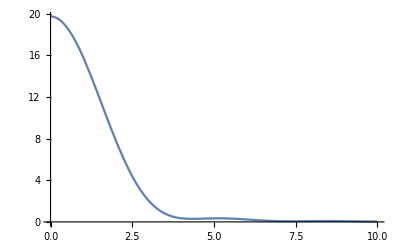

```mathematica
rm= 1
Plot[xxx, {rd, 0, 10}]
```

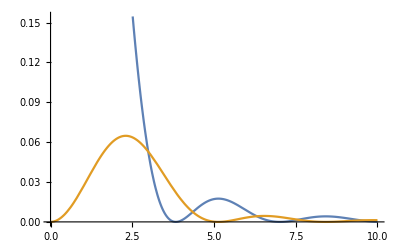

```mathematica
Plot[{4*BesselJ[1, x]^2/(x^2), 2
*BesselJ[2,x]^2/(x^2)}, {x, 0, 10}]
```

```mathematica
(* Calculate spherical harmonics coefficients *)

GG = {{aa, bb, dd}, {bb, cc, ee}, {0, 0, 0}};
s = {Cos[phi]*Sin[theta], Sin[phi]*Sin[theta], Cos[theta]};
e = GG.s
intensity = e.e
```

{dd Cos[theta]+aa Cos[phi] Sin[theta]+bb Sin[phi] Sin[theta],ee Cos[theta]+bb Cos[phi] Sin[theta]+cc Sin[phi] Sin[theta],0}

(dd Cos[theta]+aa Cos[phi] Sin[theta]+bb Sin[phi] Sin[theta])^2+(ee Cos[theta]+bb Cos[phi] Sin[theta]+cc Sin[phi] Sin[theta])^2

```mathematica
(* Expand onto constant spherical harmonics *)
I0inner = Integrate[intensity*Sin[theta], {theta, 0, Pi}]
I0 = Integrate[I0inner, {phi, 0, 2*Pi}]
```

2/3 (aa^2+2 bb^2+cc^2+dd^2+ee^2+(aa^2-cc^2) Cos[2 phi]+2 bb (aa+cc) Sin[2 phi])

4/3 (aa^2+2 bb^2+cc^2+dd^2+ee^2) π

```mathematica
Integral[BesselJ[0,x]*x, {x, 0 , Infinty}]
```

```mathematica
Integral[x *BesselJ[0,k*x],{x,0,Infinty}]
```

```mathematica
Integral[x BesselJ[1,k *x],{x,0,Infinty}]
```

```mathematica
Integral[x BesselJ[0,k x],{x,0,Infinty}]
```

Integral[x BesselJ[0,k x],{x,0,Infinty}]

```mathematica
Integral[x BesselJ[0,k x]*Exp[,{x,0,Infinty}]h
```

HankelTransform[ⅇ^-r,r,s]